# 9.1 Hmwk - Scatter Diagrams and Linear Correlation (Homework)

```mathematica
data={{3,60},{6,95},{12,140},{14,154},{26,185}};
```

```mathematica
lm=LinearModelFit[data,x,x]
```

FittedModel[62.827+5.24369 x]

```mathematica
lm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 62.827 | 15.413 | 4.07623 | 0.0266551
x | 5.24369 | 1.05807 | 4.95589 | 0.0157706

```mathematica
lm["Response"]
```

```mathematica
lm["Data"]
```

```mathematica
lm["BestFitParameters"]
```

```mathematica
lm["BasisFunctions"]
```

```mathematica
lm["BestFit"]
```

62.827+5.24369 x

```mathematica
lm["Properties"]
```

{AdjustedRSquared,AIC,AICc,ANOVATable,ANOVATableDegreesOfFreedom,ANOVATableEntries,ANOVATableFStatistics,ANOVATableMeanSquares,ANOVATablePValues,ANOVATableSumsOfSquares,BasisFunctions,BetaDifferences,BestFit,BestFitParameters,BIC,CatcherMatrix,CoefficientOfVariation,CookDistances,CorrelationMatrix,CovarianceMatrix,CovarianceRatios,Data,DesignMatrix,DurbinWatsonD,EigenstructureTable,EigenstructureTableEigenvalues,EigenstructureTableEntries,EigenstructureTableIndexes,EigenstructureTablePartitions,EstimatedVariance,FitDifferences,FitResiduals,Function,FVarianceRatios,HatDiagonal,MeanPredictionBands,MeanPredictionConfidenceIntervals,MeanPredictionConfidenceIntervalTable,MeanPredictionConfidenceIntervalTableEntries,MeanPredictionErrors,ParameterConfidenceIntervals,ParameterConfidenceIntervalTable,ParameterConfidenceIntervalTableEntries,ParameterConfidenceRegion,ParameterErrors,ParameterPValues,ParameterTable,ParameterTableEntries,ParameterTStatistics,PartialSumOfSquares,PredictedResponse,Properties,Response,RSquared,SequentialSumOfSquares,SingleDeletionVariances,SinglePredictionBands,SinglePredictionConfidenceIntervals,SinglePredictionConfidenceIntervalTable,SinglePredictionConfidenceIntervalTableEntries,SinglePredictionErrors,StandardizedResiduals,StudentizedResiduals,VarianceInflationFactors}

```mathematica
√lm["RSquared"]
```

0.944007

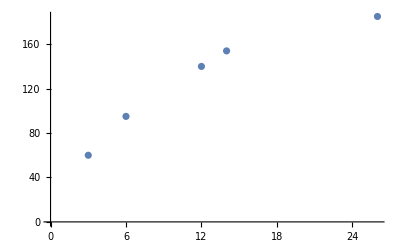

```mathematica
ListPlot[lm["Data"]]
```

## Maximum Wind Speed and Cyclone

Can a low barometer reading be used to predict maximum wind speed of an approaching tropical cyclone? For a random sample of tropical cyclones, let x be the lowest pressure (in millibars) as a cyclone approaches, and let y be the maximum wind speed (in miles per hour) of the cyclone.

```mathematica
data={{1004,40},{975,100},{992,65},{935,145},{979,76},{926,153}};
```

```mathematica
lm=LinearModelFit[data,x,x]
```

FittedModel[1474.88-1.42321 x]

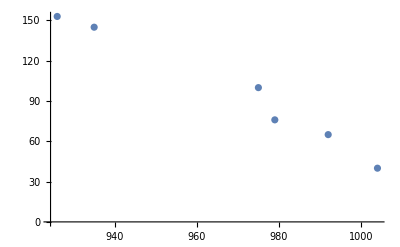

```mathematica
ListPlot[lm["Data"]]
```

```mathematica
lm["RSquared"]
```

0.975444

```mathematica
√lm["RSquared"]
```

0.987646

```mathematica
AssociationMap[lm[#]&,lm["Properties"]]
```

<|AdjustedRSquared→0.969305,AIC→45.8268,AICc→57.8268,ANOVATable→ | DF | SS | MS | F-Statistic | P-Value
x | 1 | 9911.98 | 9911.98 | 158.895 | 0.000227995
Error | 4 | 249.523 | 62.3807 |  | 
Total | 5 | 10161.5 |  |  | ,ANOVATableDegreesOfFreedom→{1,4,5},ANOVATableEntries→{{1,9911.98,9911.98,158.895,0.000227995},{4,249.523,62.3807},{5,10161.5}},ANOVATableFStatistics→{158.895},ANOVATableMeanSquares→{9911.98,62.3807},ANOVATablePValues→{0.000227995},ANOVATableSumsOfSquares→{9911.98,249.523,10161.5},BasisFunctions→{1,x},BetaDifferences→{{0.650119,-0.666205},{-0.299149,0.343823},{-0.096887,0.100532},{0.0734198,-0.0716505},{0.112644,-0.12252},{-0.627831,0.6159}},BestFit→1474.88-1.42321 x,BestFitParameters→{1474.88,-1.42321},BIC→45.2021,CatcherMatrix→{{-6.85934,-1.11978,-4.48435,6.79684,-1.91145,8.57808},{0.00725452,0.00132829,0.00480229,-0.00684582,0.0021457,-0.00868499}},CoefficientOfVariation→0.0818461,CookDistances→{0.366233,0.335887,0.0163369,0.00588331,0.0712139,0.316711},CorrelationMatrix→{{1.,-0.999566},{-0.999566,1.}},CovarianceMatrix→{{11967.6,-12.3461},{-12.3461,0.0127477}},CovarianceRatios→{1.74341,0.0949856,2.36468,2.917,1.57451,2.8508},Data→{{1004,40},{975,100},{992,65},{935,145},{979,76},{926,153}},DesignMatrix→{{1.,1004.},{1.,975.},{1.,992.},{1.,935.},{1.,979.},{1.,926.}},DurbinWatsonD→2.05135,EigenstructureTable→Eigenvalue | Index | x
1. | 1. | 1.,EigenstructureTableEigenvalues→{1.},EigenstructureTableEntries→{{1.,1.,1.}},EigenstructureTableIndexes→{1.},EigenstructureTablePartitions→{{1.}},EstimatedVariance→62.3807,FitDifferences→{-0.855019,1.54926,0.158216,0.0941527,-0.355044,-0.742034},FitResiduals→{-5.97589,12.7509,1.94554,0.822315,-5.55625,-3.98661},Function→(1474.88-1.42321 #1&),FVarianceRatios→{1.74006,0.339376,1.81166,2.19761,1.39352,2.47811},HatDiagonal→{0.424202,0.175301,0.27952,0.396001,0.189197,0.535779},MeanPredictionBands→{1474.88-1.42321 x-2.77645 √(11967.6-24.6922 x+0.0127477 x^2),1474.88-1.42321 x+2.77645 √(11967.6-24.6922 x+0.0127477 x^2)},MeanPredictionConfidenceIntervals→{{31.6935,60.2583},{78.0678,96.4304},{51.4608,74.6481},{130.378,157.977},{72.018,91.0945},{140.935,173.038}},MeanPredictionConfidenceIntervalTable→Observed | Predicted | Standard Error | Confidence Interval
40 | 45.9759 | 5.14413 | {31.6935,60.2583}
100 | 87.2491 | 3.30687 | {78.0678,96.4304}
65 | 63.0545 | 4.17573 | {51.4608,74.6481}
145 | 144.178 | 4.9702 | {130.378,157.977}
76 | 81.5562 | 3.43544 | {72.018,91.0945}
153 | 156.987 | 5.7812 | {140.935,173.038},MeanPredictionConfidenceIntervalTableEntries→{{40,45.9759,5.14413,{31.6935,60.2583}},{100,87.2491,3.30687,{78.0678,96.4304}},{65,63.0545,4.17573,{51.4608,74.6481}},{145,144.178,4.9702,{130.378,157.977}},{76,81.5562,3.43544,{72.018,91.0945}},{153,156.987,5.7812,{140.935,173.038}}},MeanPredictionErrors→{5.14413,3.30687,4.17573,4.9702,3.43544,5.7812},ParameterConfidenceIntervals→{{1171.15,1778.62},{-1.73669,-1.10974}},ParameterConfidenceIntervalTable→ | Estimate | Standard Error | Confidence Interval
1 | 1474.88 | 109.397 | {1171.15,1778.62}
x | -1.42321 | 0.112906 | {-1.73669,-1.10974},ParameterConfidenceIntervalTableEntries→{{1474.88,109.397,{1171.15,1778.62}},{-1.42321,0.112906,{-1.73669,-1.10974}}},ParameterConfidenceRegion→FittedModels`ParameterEllipsoid[{1474.88,-1.42321},{407.692,0.0124019},{{-0.999999,0.00103163},{-0.00103163,-0.999999}}],ParameterErrors→{109.397,0.112906},ParameterPValues→{0.000175135,0.000227995},ParameterTable→ | Estimate | Standard Error | t-Statistic | P-Value
1 | 1474.88 | 109.397 | 13.482 | 0.000175135
x | -1.42321 | 0.112906 | -12.6054 | 0.000227995,ParameterTableEntries→{{1474.88,109.397,13.482,0.000175135},{-1.42321,0.112906,-12.6054,0.000227995}},ParameterTStatistics→{13.482,-12.6054},PartialSumOfSquares→{9911.98},PredictedResponse→{45.9759,87.2491,63.0545,144.178,81.5562,156.987},Properties→{AdjustedRSquared,AIC,AICc,ANOVATable,ANOVATableDegreesOfFreedom,ANOVATableEntries,ANOVATableFStatistics,ANOVATableMeanSquares,ANOVATablePValues,ANOVATableSumsOfSquares,BasisFunctions,BetaDifferences,BestFit,BestFitParameters,BIC,CatcherMatrix,CoefficientOfVariation,CookDistances,CorrelationMatrix,CovarianceMatrix,CovarianceRatios,Data,DesignMatrix,DurbinWatsonD,EigenstructureTable,EigenstructureTableEigenvalues,EigenstructureTableEntries,EigenstructureTableIndexes,EigenstructureTablePartitions,EstimatedVariance,FitDifferences,FitResiduals,Function,FVarianceRatios,HatDiagonal,MeanPredictionBands,MeanPredictionConfidenceIntervals,MeanPredictionConfidenceIntervalTable,MeanPredictionConfidenceIntervalTableEntries,MeanPredictionErrors,ParameterConfidenceIntervals,ParameterConfidenceIntervalTable,ParameterConfidenceIntervalTableEntries,ParameterConfidenceRegion,ParameterErrors,ParameterPValues,ParameterTable,ParameterTableEntries,ParameterTStatistics,PartialSumOfSquares,PredictedResponse,Properties,Response,RSquared,SequentialSumOfSquares,SingleDeletionVariances,SinglePredictionBands,SinglePredictionConfidenceIntervals,SinglePredictionConfidenceIntervalTable,SinglePredictionConfidenceIntervalTableEntries,SinglePredictionErrors,StandardizedResiduals,StudentizedResiduals,VarianceInflationFactors},Response→{40,100,65,145,76,153},RSquared→0.975444,SequentialSumOfSquares→{9911.98},SingleDeletionVariances→{62.5008,17.4593,81.4231,82.8011,70.4824,71.7623},SinglePredictionBands→{1474.88-1.42321 x-2.77645 √(12030.-24.6922 x+0.0127477 x^2),1474.88-1.42321 x+2.77645 √(12030.-24.6922 x+0.0127477 x^2)},SinglePredictionConfidenceIntervals→{{19.8061,72.1457},{63.4758,111.022},{38.2495,87.8594},{118.268,170.087},{57.6429,105.47},{129.811,184.162}},SinglePredictionConfidenceIntervalTable→Observed | Predicted | Standard Error | Confidence Interval
40 | 45.9759 | 9.42564 | {19.8061,72.1457}
100 | 87.2491 | 8.56248 | {63.4758,111.022}
65 | 63.0545 | 8.93406 | {38.2495,87.8594}
145 | 144.178 | 9.33186 | {118.268,170.087}
76 | 81.5562 | 8.61295 | {57.6429,105.47}
153 | 156.987 | 9.7879 | {129.811,184.162},SinglePredictionConfidenceIntervalTableEntries→{{40,45.9759,9.42564,{19.8061,72.1457}},{100,87.2491,8.56248,{63.4758,111.022}},{65,63.0545,8.93406,{38.2495,87.8594}},{145,144.178,9.33186,{118.268,170.087}},{76,81.5562,8.61295,{57.6429,105.47}},{153,156.987,9.7879,{129.811,184.162}}},SinglePredictionErrors→{9.42564,8.56248,8.93406,9.33186,8.61295,9.7879},StandardizedResiduals→{-0.997108,1.77774,0.290205,0.133966,-0.781266,-0.740827},StudentizedResiduals→{-0.996149,3.36031,0.254013,0.116279,-0.734994,-0.690707},VarianceInflationFactors→{0.,1.}|>